The roots of Gaussian analytic functions for the complex plane, C.  As I degree of the polynomial N, the roots are supported in a circle of radius √N leading to a translation invariant process in the plane in the large N limit.

math.PR/0310297 Zeros of the i.i.d. Gaussian power series: a conformally invariant determinantal process. Yuval Peres, Balint Virag
math.CV/0410343 Zeroes of Gaussian analytic functions. Mikhail Sodin.

```mathematica
gs[]:= RandomReal[NormalDistribution[0,1/2]];
plotroots[f_]:=(rts = NSolve[f[z]==0,z];
pts = {Re[z],Im[z]} /. rts;
ListPlot[pts, AspectRatio-> Automatic])
```

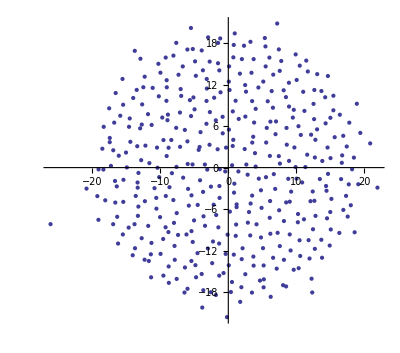

```mathematica
f[z_]:= Sum[(gs[]+I gs[])z^k/Sqrt[k!],{k,0,400}];
plotroots[f]
```

The analogous process in the unit disc, has roots proportional to hyperbolic area in the unit disc, D.  With our Euclidean eyes, it looks like roots are concentrated at the edge of the unit circle.  Introducing a parameter [rho], the plane process is the scaling limit of the unit disc process as N -> infinity.  
Since this particular process is conformally invariant, it can be mapped to any domain in the complex plane. [Haven't tried this yet.]

```mathematica
choose[x_,n_]:= Product[x-k,{k,0,n-1}]/n!
```

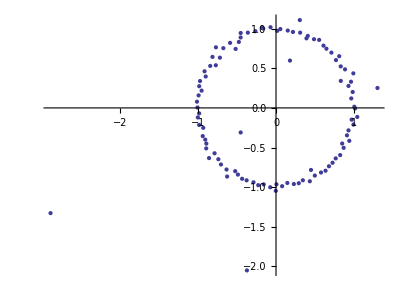

```mathematica
rho=1;
f[z_]:= Sum[(gs[]+I gs[])Sqrt[choose[-rho,n]]z^n,{n,0,100}];
plotroots[f]
```

Change the paramter rho

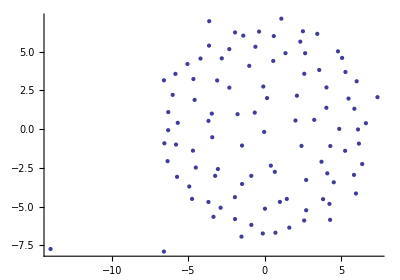

```mathematica
rho=100;
f= Sum[(gs[]+I gs[])Sqrt[choose[-rho,n]]z^n,{n,0,100}];
NSolve[f==0,z];
Sqrt[rho]{Re[z],Im[z]} /. %;
ListPlot[%, AspectRatio-> Automatic]
```